## Maximum copula

```mathematica
SeedRandom[];
```

```mathematica
U={};A=10;
Timing[For[i=0,i<2000,i++,
x=RandomReal[];
y=f1[x,RandomReal[],A];
z=f2[x,y,RandomReal[],A];
AppendTo[U,{x,y,z}]]]
ListPointPlot3D[U,AspectRatio->1]
```

{1.282,Null}

-Graphics3D-

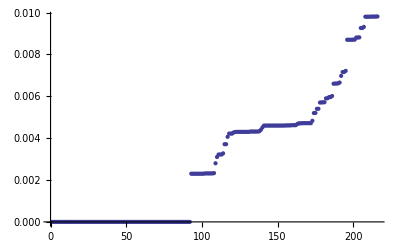

```mathematica
M={};m={};l=Length[U];h=1/5;
For[i=0,i≤1,i+=h,
For[j=0,j≤1,j+=h,
For[k=0,k≤1,k+=h,
AppendTo[m,Length[Select[U,#[[1]]≤i && #[[2]]≤j&& #[[3]]≤k&]]/l-c[i,j,k,A]//N]
]
]];m=Sort[m];ListPlot[m]
```

```mathematica
CForm[ⅇ^(-(-(-Log[x])^a+((-1+a) ProductLog[((-x Z2 (-Log[x])^-a Log[x])^(-1/(-1+a)))/(-1+a)])^a)^(1/a))]
```

Power(E,-Power(-Power(0.1730846177216665,a) + 
      Power((-1 + a)*ProductLog(1/
          (Power(0.14557566371451522,1/(-1 + a))*(-1 + a)*
            Power(Z2/Power(0.1730846177216665,a),1/(-1 + a)))),a),1/a))

```mathematica
CForm[For[i=0,i<2000,i++,

]]
```

Null

# FUnction Definitions

```mathematica
Exit[]
```

```mathematica
$Assumptions=a>1 && 0<Z<1 && 0<x<1&& 0<y<1&& 0<z<1&& 0<Z1<1&& 0<Z2<1&& A>1
```

```mathematica
c[x_,y_,z_,a_]:=Exp[-((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)]
```

```mathematica
Simplify[D[c[x,y,1,a],x]]
```

```mathematica
Solve[%==Z2,y]
```

```mathematica
f1=Compile[{{x,_Real},{Z2,_Real},{a,_Real}},ⅇ^(-(-(-Log[x])^a+((-1+a) ProductLog[((-x Z2 (-Log[x])^-a Log[x])^(-1/(-1+a)))/(-1+a)])^a)^(1/a))];
```

```mathematica
Simplify[D[D[c[x,y,z,a],x],y]/D[D[c[x,y,1,a],x],y]]
```

```mathematica
ddc[x_,y_,z_,a_]:=(ⅇ^(((-Log[x])^a+(-Log[y])^a)^(1/a)-((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)) (-1+a+((-Log[x])^a+(-Log[y])^a+(-Log[z])^a)^(1/a)) (((-Log[x])^a+(-Log[y])^a)/((-Log[x])^a+(-Log[y])^a+(-Log[z])^a))^(2-1/a))/(-1+a+((-Log[x])^a+(-Log[y])^a)^(1/a))
```

```mathematica
f2[x_,y_,z3_,a_]:=FindRoot[ddc[x,y,z,a]-z3,{z,0.0000000000001,1},Method->"Brent"][[1,2]]
```

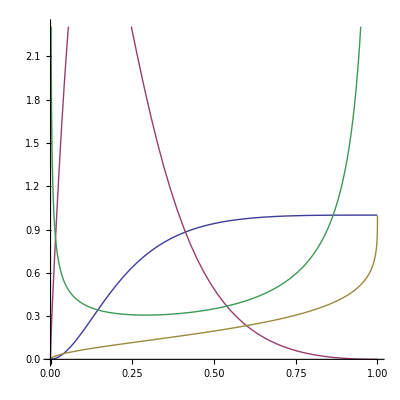

```mathematica
aa=3.00001;xx=0.1;yy=0.7;Plot[{ddc[xx,yy,y,aa],D[ddc[xx,yy,sy,aa],sy]/.sy->y,f2[xx,yy,y,aa],Simplify[Simplify[1/D[ddc[xx,yy,sy,aa],sy]]/.sy->f2[xx,yy,y,aa]]},{y,0,1},AspectRatio->1]
```

```mathematica
y=.
```

```mathematica
f2[xx,yy,y,aa]
```

FindRoot::nlnum: The function value {2.00524×10^-17 - 1.\ y} is not a list of numbers with dimensions {1} at {z} = {1.×10^-13}.

-y

```mathematica
Simplify[Simplify[1/D[ddc[xx,yy,sy,aa],sy]]/.sy->f2[xx,yy,y,aa]]
```

FindRoot::nlnum: The function value {2.00524×10^-17 - 1.\ y} is not a list of numbers with dimensions {1} at {z} = {1.×10^-13}.

-(ⅇ^((12.2535+(-Log[-y])^3.00001)^0.333332) y (12.2535+(-Log[-y])^3.00001)^0.666668)/(((151.703+151.702 (12.2535+(-Log[-y])^3.00001)^0.333332) (1/(12.2535+(-Log[-y])^3.00001))^1.66667+(1517.03 (12.2535+(-Log[-y])^3.00001)^0.666668+758.511 (12.2535+(-Log[-y])^3.00001)^1.) (1/(12.2535+(-Log[-y])^3.00001))^2.66667) (-Log[-y])^2.00001)

```mathematica
c2[x,y,z]
```

c2[0.124265,0.107698,0.0986968]

```mathematica
Animate[Plot3D[c[x,y,z,3],{x,0,1},{z,0,1}],{y,0,1}]
```

```mathematica
c2[
```

c2